## Mathematica’s Core Language

Hello and welcome to our 2nd section: Programming with Mathematica. Congratulations on having made it this far!

In the previous section we made use of quite a bit of Mathematica’s built-in functionalities to make graphics and animations. We wanted our first section to be fun and useful.

In order to truly harness Mathematica’s power, we need to learn Mathematica’s core programming language. In this lesson, we’ll take account of what we’ve seen so far, and give you an overview of the core language ideas, which we’ll expand upon in subsequent lessons.

### Expressions

Everything in Mathematica is an Expression. Arithmetic operators are expressions:

```mathematica
3+x+x^2
```

3+x+x^2

Lists are expressions:

```mathematica
{1,2,3}
```

{1,2,3}

Plots are expressions:

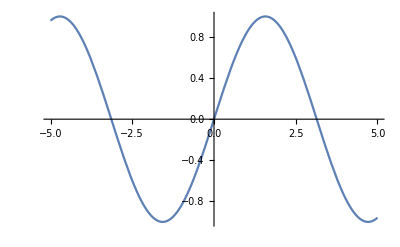

```mathematica
Plot[Sin[x],{x,-5,5}]
```

Even the graphic objects (the plot above) are expressions.

The function FullForm enables us to see the expression in its full form:

```mathematica
?FullForm
```

RowBox[{"FullForm", "[", StyleBox["expr", "TI"], "]"}] prints as the full form of StyleBox["expr", "TI"], with no special syntax.

For example:

```mathematica
FullForm[3+x]
```

Plus[3,x]

Here we can see that the Head of this expression is Plus, and its arguments are 3 and x.

Let’s try another one:

```mathematica
FullForm[2+x+x^2]
```

Plus[2,x,Power[x,2]]

The Head of this expression is also Plus, but note that the third argument is a nested expression whose head is Power and whose arguments are x and 2.

### Lists

Throughout section 1, we used Lists for various things. For instance, when we defined the domain over which to plot Sin:

```mathematica
Plot[Sin[x],{x,-5,5}]
```

-Graphics-

Here, the domain of x, from -5 to 5 is enclosed in a list.

In previous lectures we generated Lists using Range and Table, and plotted the data using ListPlot and ListLinePlot. We used Lists to:

Group arguments that we passed to Manipulate

Pass multiple graphics to GraphicsRow

Pass rows and columns of graphics to GraphicsGrid

Based on this, it may not come as a surprise to you that Lists are a fundamental object in Mathematica. In our lecture on Lists, we’ll review how to generate lists using functions like Range and Table.

We’ll also look at:

How to access specific elements and ranges of elements in a list using Part, Span and other related functions.

How to add and remove elements from a List.

How you can use Lists as sets.

And how to rearrange, group, combine, and sort Lists.

### Rules and Patterns

Before we introduce how to define functions in Mathematica, we need to look at Rules and Patterns.

Patterns are a way to enable Mathematica to represent classes of expressions. For example, the pattern:

```mathematica
x^_
```

Represents the expression x to any power. Here, _ is a wildcard. We will need these ideas in order to define functions.

Rules provide a way to represent a transformation. For example, if you had the expression:

```mathematica
3+x+x^2
```

3+x+x^2

And wanted to evaluate the expression at x = 3, you could do so as follows:

```mathematica
3+x+x^2/.x->3
```

15

The use of Rules becomes very powerful when combined with Patterns and we will examine them in great detail in the Rules and Patterns lecture.

We have already used rules in our first section, when we needed to add an option to a function:

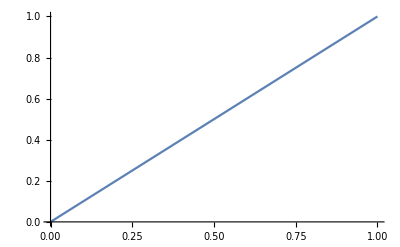

```mathematica
Plot[x,{x,0,1},PlotRange->Automatic]
```

We used the rule PlotRange → Automatic.

### Functions

We’ve been using Functions since the beginning of our course. In our lecture on functions, you will learn:

How to define functions using Patterns

How to scope variables using the functions Module and Block

And how to define pure functions

### Tying it all together

Once we have all the basic pieces in place, we’ll see how to be a productive programmer in Mathematica by combining all the knowledge we’ve learned so far.

No course in any programming language would be complete without coverage of Strings and String Manipulation as well as reading and writing files.